```mathematica
ClearAll["Global`*"]
```

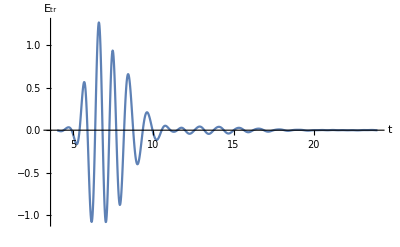

```mathematica
messyData=Import["C:\\Users\\79511\\OneDrive\\Документы\\GitHub\\Labs_Zalipaev\\lab_5\\epsdata.txt"];
lessMessyData=ToExpression@StringReplace[StringSplit[messyData],"e"->"*10^"];
data=Table[{lessMessyData[[i]],lessMessyData[[i+1]]},{i,1,Length[lessMessyData]-1,2}];
tmin=data[[1,1]];
tmax=data[[-1,1]];
ListLinePlot[data,PlotRange->All,AxesLabel->{"t","E_tr"}]
```

```mathematica
(*f[t_]:=Exp[-t^2/(4 Subscript[τ, p]^2)-I Subscript[ω, 0] t]
F[ω_]:=Integrate[Exp[I ω t] f[t],{t,-Infinity,Infinity}][[1]]*
```

```mathematica
z=10^-3;(*detector position*)
c=3*10^8;
factor=N@2 Pi z/c*10^11;
```

```mathematica
F[f_,τ_,f0_]:=2Sqrt[Pi] τ Exp[-2Pi (f-f0)^2 τ^2]
Etr[t_]:=Interpolation[data][t]
T[f_]:=(F[f,1,1])^(-1)*Integrate[Exp[I (f t-factor)]*Etr[t],{t,tmin,tmax}]
```

```mathematica
Table[N@T[i],{i,0,2.2,0.1}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {10.0483}. NIntegrate obtained -0.000409668-0.000709566 ⅈ and 7.78293×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {10.0483}. NIntegrate obtained 0.000369792-0.000343297 ⅈ and 7.85457×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {10.0483}. NIntegrate obtained -0.0000823334-0.000253332 ⅈ and 7.85578×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{-0.0618842-0.107187 ⅈ,0.0169294-0.0157165 ⅈ,-0.00129531-0.00398553 ⅈ,0.00379911-0.00356692 ⅈ,0.00185838+0.00105338 ⅈ,0.00027906+0.000161272 ⅈ,0.000595339+0.000389611 ⅈ,-0.0000722+0.000550126 ⅈ,-0.000117145+0.000150618 ⅈ,-0.000105504+0.000299571 ⅈ,-0.000408408+0.000118804 ⅈ,-0.000265876-0.0000964753 ⅈ,-0.000476248-0.0000345033 ⅈ,-0.000662039-0.000767322 ⅈ,-0.0000746998-0.00116443 ⅈ,-0.000578023-0.00234326 ⅈ,0.0030934-0.0070669 ⅈ,0.012486-0.00727557 ⅈ,0.0331279-0.0246555 ⅈ,0.195469-0.0144879 ⅈ,0.500302+0.282861 ⅈ,2.32675+0.986306 ⅈ,10.9142+14.7168 ⅈ}

```mathematica
k0=1;
d=1;
Φ[n_]:=(4n)/((n+1)^2 Exp[-I k0 n d]-(n-1)^2 Exp[I k0 n d])-T[f]
Eliminate[Φ[n],{n,0}]
```

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {n} = {0.}.

FindRoot[Φ[n],{n,0}]

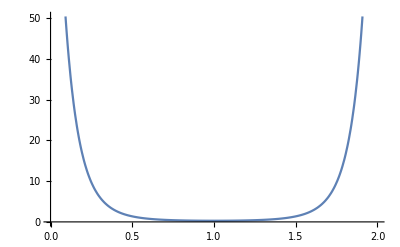

```mathematica
F[f_,τ_,f0_]:=2Sqrt[Pi] τ Exp[-2Pi (f-f0)^2 τ^2]
Plot[(F[f,1,1])^-1,{f,0,2}]
```

```mathematica
FindFormula[data,x,PerformanceGoal->"Quality"]
```

-0.154905 Sin[6.45641 x]

```mathematica
NonlinearModelFit[data,Sin[k x]Exp[l+m x^2],{k,l,m},x]
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FittedModel[ⅇ^(-99.+1. x^2) Sin[1. x]]

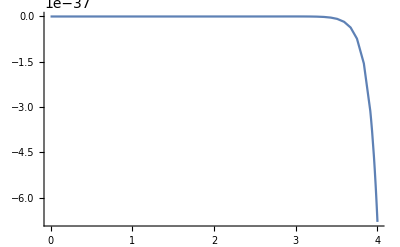

```mathematica
Plot[ⅇ^(-99.00000000002063+1.0000000000000364 x^2) Sin[1.00000000000007 x],{x,0,4},PlotRange->All]
```